

```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
Manipulate[
	Plot[Sin[x *frequency], {x,0,2π}],
	{frequency,1,5}
]
```

```mathematica
Manipulate[
		Plot[Sin[frequency*x+phase],{x,0,2π}],
		{frequency,1,5},
		{phase,1,10}
]
```

```mathematica
Manipulate[
	Plot[function[frequency*x+phase],{x,0,2*π}],
	{frequency,1,5},
	{phase,1,10},
	{function,{Sin,Cos,Tan}}
]
```

```mathematica
Manipulate[
	Plot[function[frequency*x*phase],{x,0,2*π}],
	{frequency,1,5},
	{phase,1,10},
	{function,{Sin,Cos,Tan,Csc}}
]
```

```mathematica
Manipulate[
	Plot[function[frequency*x*phase],{x,0,2*π}],
	{frequency,1,5},
	{phase,1,10},
	{function,{Sin,Cos,Tan,Csc},ControlType->RadioButton}
]
```

```mathematica
Manipulate[
	Expand[{a+b}^n],
	{n,1,10,1}
]
```

```mathematica
(* 创建好模型的一些窍门 *)
```

```mathematica
Manipulate[
	Plot[a*Sin[x],{x,0,2π},PlotRange->{-10,10}], (*PlotRange的参数以列表的形式给出*)
	{a,1,10}
]
```

```mathematica
Manipulate[
	Plot3D[
		Sin[a x y],
		{x,-2,2},
		{y,-2,2}
	],
{a,-5,5}
]
```

```mathematica
Manipulate[
	Plot3D[
	Sin[a x y],
	{x,-2,2},
	{y,-2,2},
	PerformanceGoal->"Quality"
   ],
      {a,1,5}
     
]
```

```mathematica
Manipulate[
	Plot[fn[f*x+ps],{x,0,2π}],
	{{f,1,"frequency"},1,5},
	{{ps,1,"phase shift"},1,10},
	{{fn,Sin,"function"},{Sin,Cos,Tan,Cot,Csc}}
]
```

```mathematica
Manipulate[
	Plot[fn[f*x+ps],{x,0,2π}],
	{{f,1,"frequency"},1,5,Appearance->"Labeled"},
	{{ps,1,"phase shift"},1,10,Appearance->"Labeled"},
	{{fn,Sin,"function"},{Sin,Cos,Tan,Cot,Csc,Sec}}
]
```

```mathematica
(* 交互式绘图标签 *)
Manipulate[
	Plot[Sin[f*x],{x,0,2π}],
	{{f,1,"frequency"},1,5,Appearance->"Labeled"}
]
```

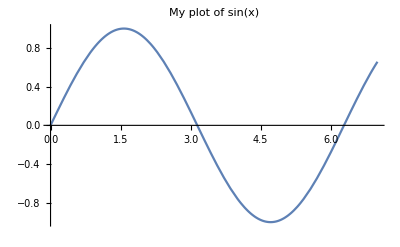

```mathematica
Plot[
	Sin[x],
	{x,0,7},
	PlotLabel-> "My plot of sin(x)"	
]
```

```mathematica
Plot[
	Sin[x],
	{x,0,7},
	PlotLabel-> "My plot of"<>" sin(x)"	
]
```

-Graphics-

```mathematica
Manipulate[
	Plot[
	Sin[f*x],{x,0,2π},
	PlotLabel-> "sin("<>ToString[f]<>"x)"
],
{{f,1,"frequency"},1,5}
]
```

```mathematica
Manipulate[
	Plot[
		Sin[f*x+ps],{x,0,2π},
		PlotLabel->"sin("<>ToString[f]<>"x)"
	],
	{{f,1,"frequency"},1,5,Appearance->"Labeled"},
	{{ps,1,"phase shift"},1,6,Appearance->"Labeled"}
]
```

```mathematica
Manipulate[
	Plot[
	a*Sin[f*x+ps],
	{x,0,2π},
	PlotRange->{-4,6}
   ],
      {{f,1,"frequency"},1,5,Appearance->"Labeled"},
      {{a,3,"amplitude"},1,5,Appearance->"Labeled"},
      {{ps,0,"phase shift"},0,2π,Appearance->"Labeled"}
]
```

```mathematica
(* 记住用户自定义的函数 *)
f[x_] := 2 x^2+2x+1;
```

```mathematica
Manipulate[
	Plot[f[a*x],{x,-4,4}],
	{a,-1,1}
]
```

```mathematica
Manipulate[
	Plot[g[a*x],{x,-4,4}],
	{a,-1,1},
	Initialization:>(g[x_] := x^2 + 2x+1)
]
```

```mathematica
(* 保存Manipulation中符号的定义到其他文档中 *)
Manipulate[
	Plot[f[a * x],{x,-4,4}],
	{a,-1,1},
	Initialization:>(f[x_] := Sin[x]),
	SaveDefinitions->True
]
```